# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Entropy/Calculations/T1 positive parity/T1 FINAL/QMB_offline.wl"];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

# T1

```mathematica
L=8;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
g=0.05;
h=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

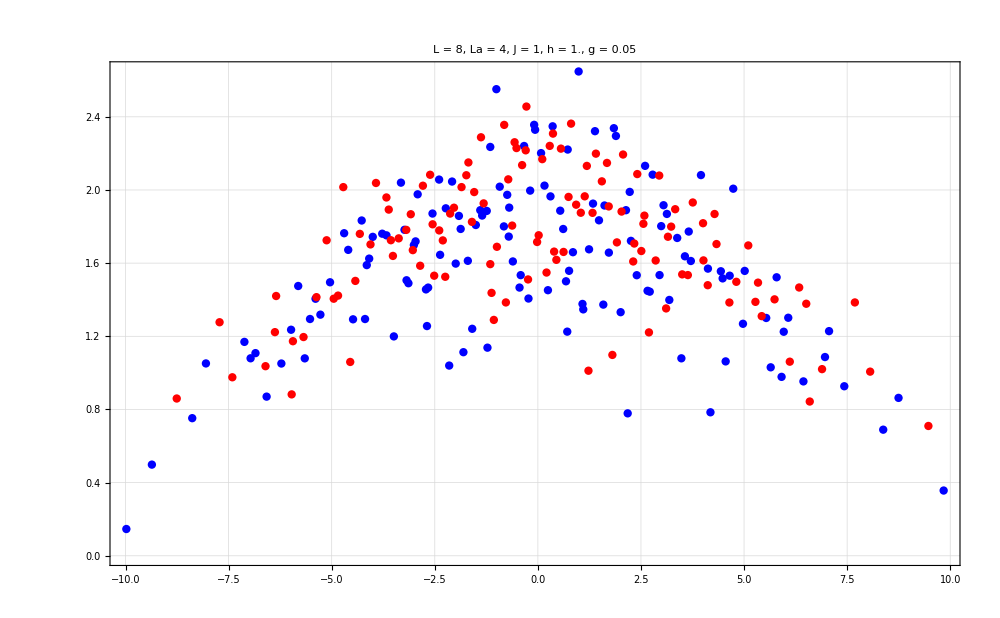

```mathematica
ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Blue,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

# L = 8, h = 1, minimum g = 0.05

```mathematica
ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Blue,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

-Graphics-

```mathematica
tlist=Table[10^i,{i,0,4,0.0010}];
tlist//Length
```

4001

```mathematica
tlist=Table[i,{i,0,500,0.1}];
tlist//Length
```

5001

```mathematica
allstates=Table[RandomChainProductState[L],100];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]];
```

```mathematica
allstates=Table[RandomChainProductState[L],500];
probs=ParallelTable[Quiet[StandardDeviation[Abs[Conjugate[allvecs].i]^2]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{probs,allstates}],First];
productstatesfull=data[[All,2]];
```

```mathematica
svntproductfull=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstatesfull},{t,tlist},DistributedContexts->Full,Method->"CoarsestGrained"];
```

## Full RPS vs Positive parity, full RPS

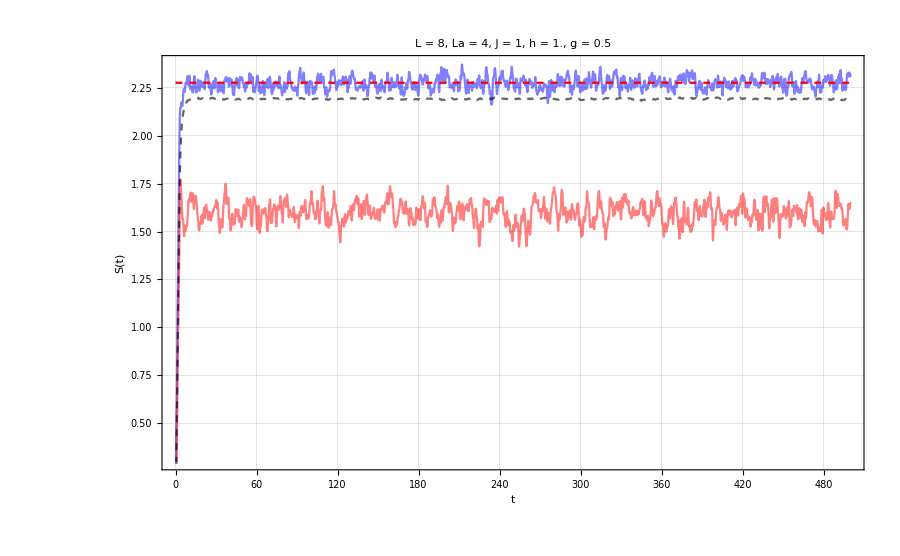

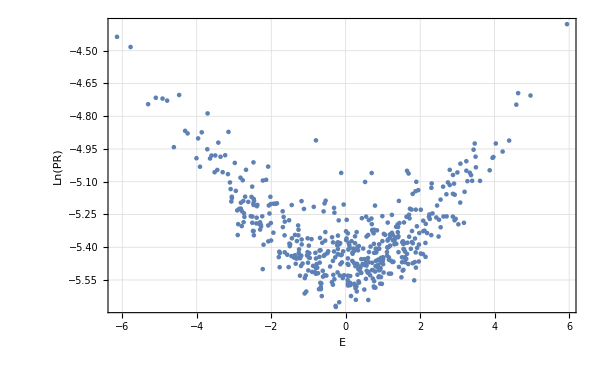

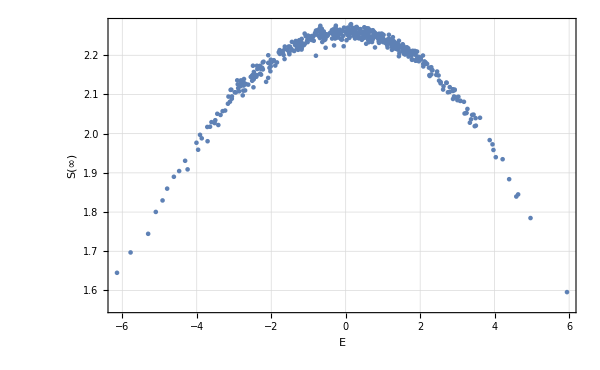

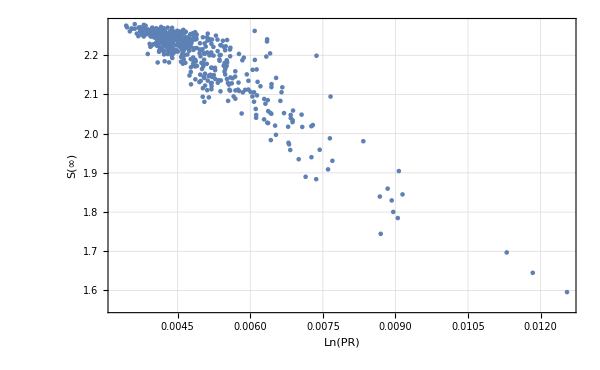

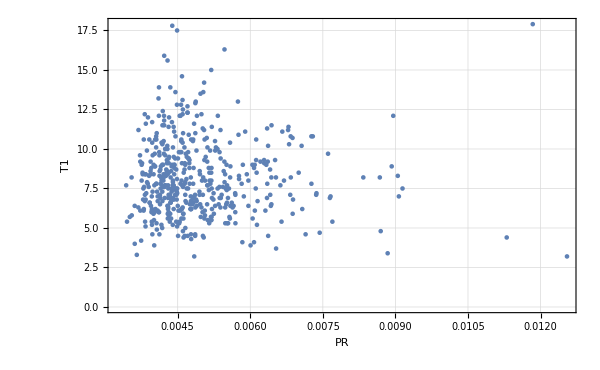

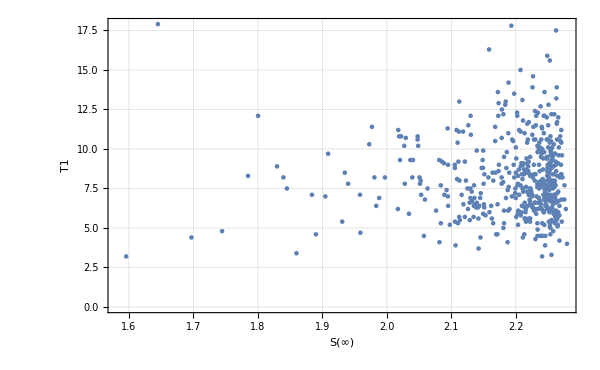

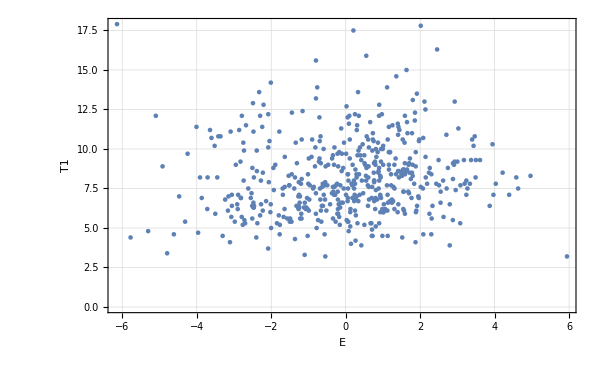

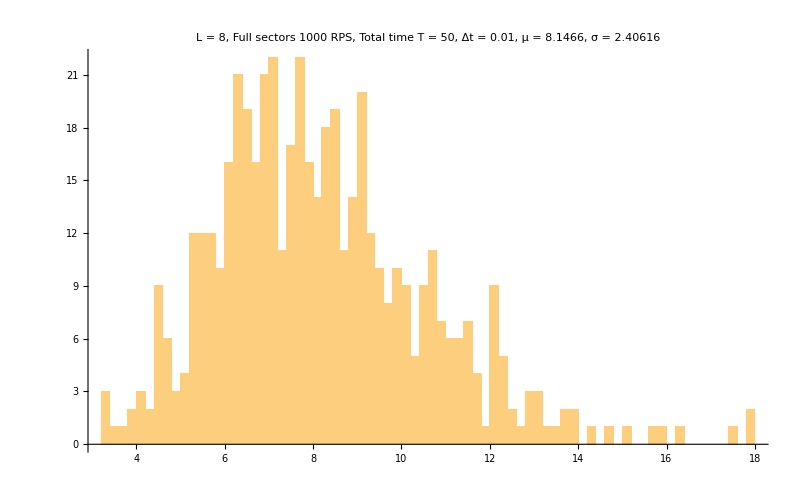

```mathematica
Show[{ListPlot[{svntproductfull[[1]],svntproductfull[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],ListPlot[Mean[svntproductfull],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproductfull[[j]];
times=tlist;
series=list[[All,2]];
limit=Mean[series[[-1000;;-1]]];
position=FirstPosition[series-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstatesfull]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstatesfull},DistributedContexts->Full];
infofull=Transpose[{sortediprs,t1s,limits,energies,productstatesfull}];
unsortedlimits=infofull[[All,3]];
ListPlot[Transpose[{infofull[[All,4]],Log[infofull[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["Ln(PR)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,4]],infofull[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["S(∞)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,1]],infofull[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["Ln(PR)",20,Black],Style["S(∞)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,1]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["PR",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,3]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["S(∞)",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,4]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
Histogram[infofull[[All,2]],50,PlotRange->All,ImageSize->800,PlotLabel->Style["L = 8, Full sectors 1000 RPS, Total time T = 50, Δt = 0.01, μ = "<>ToString[Mean[infofull[[All,2]]]]<>", σ = "<>ToString[StandardDeviation[infofull[[All,2]]]],20,Black]]
```

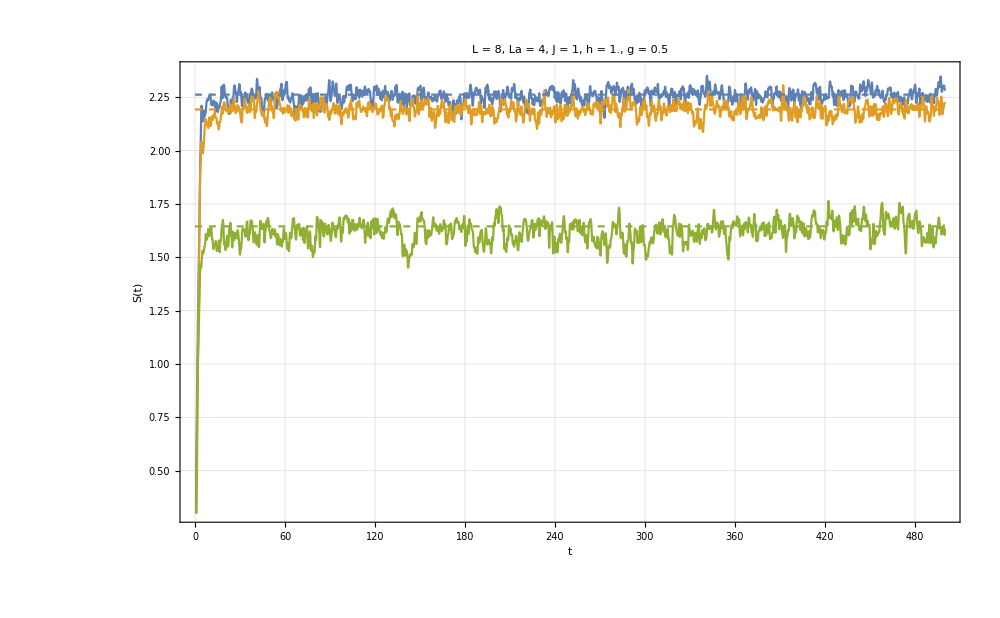

```mathematica
FAKEINFO=SortBy[Transpose[{t1s,sortediprs,limits,energies,productstatesfull,svntproductfull}],First];
fakelimits=FAKEINFO[[All,3]];
Show[{ListPlot[{FAKEINFO[[-3,6]],FAKEINFO[[-2,6]],FAKEINFO[[-1,6]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],Plot[{fakelimits[[-3]],fakelimits[[-2]],fakelimits[[-1]]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Dashed]}]
```

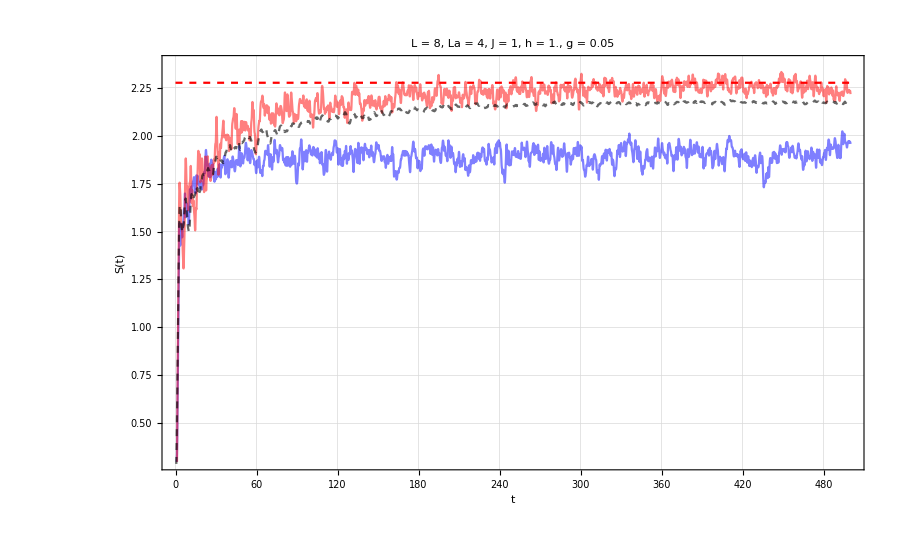

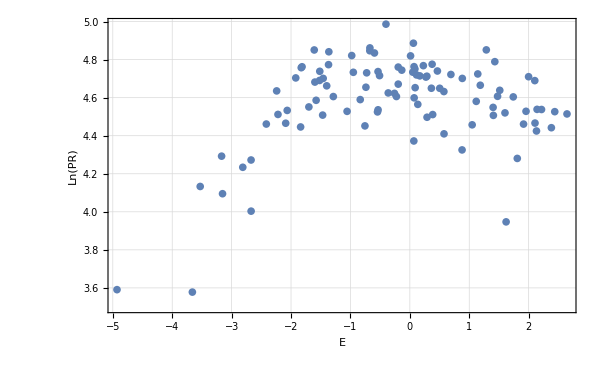

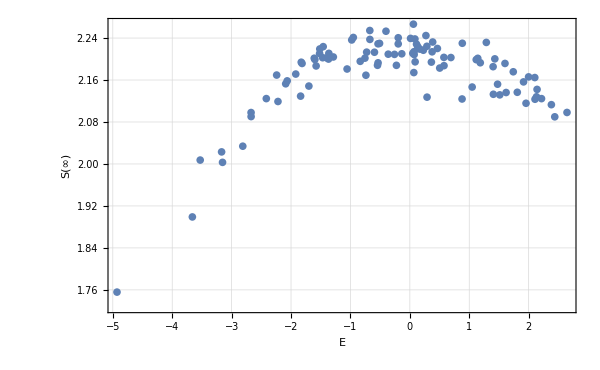

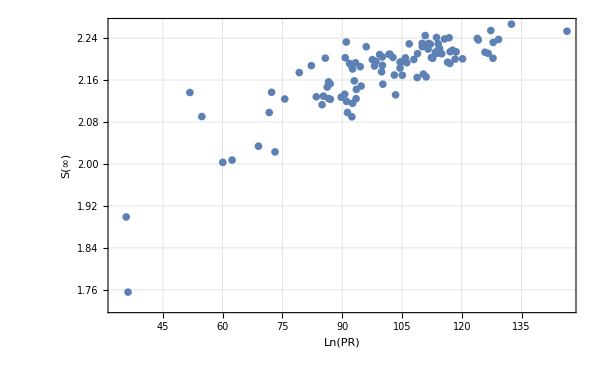

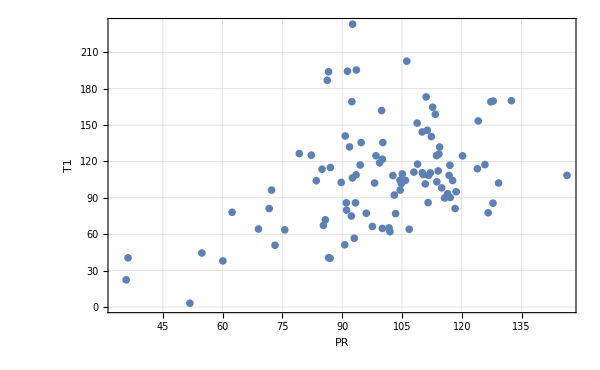

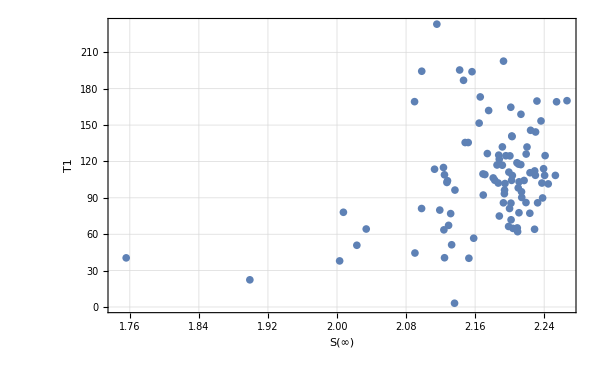

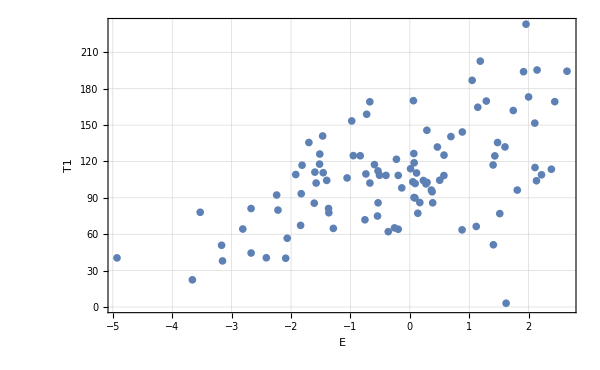

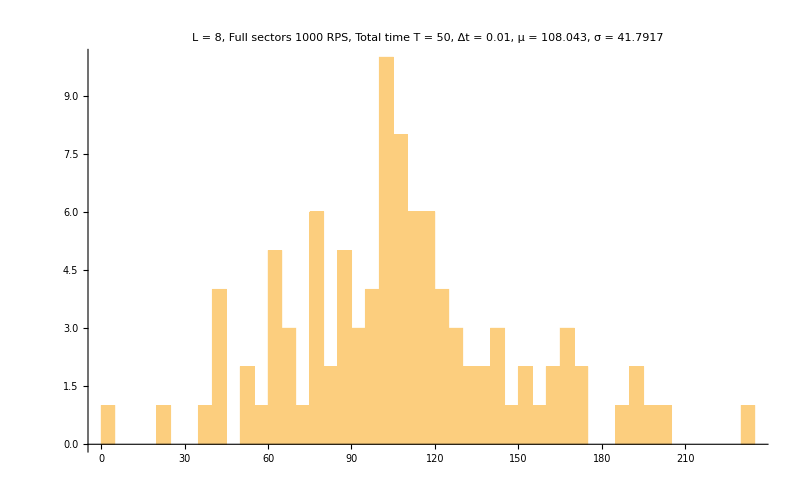

```mathematica
Show[{ListPlot[{svntproductfull[[1]],svntproductfull[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],ListPlot[Mean[svntproductfull],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproductfull[[j]];
times=tlist;
series=list[[All,2]];
limit=Mean[series[[-1000;;-1]]];
position=FirstPosition[series-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstatesfull]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstatesfull},DistributedContexts->Full];
infofull=Transpose[{sortediprs,t1s,limits,energies,productstatesfull}];
unsortedlimits=infofull[[All,3]];
ListPlot[Transpose[{infofull[[All,4]],Log[infofull[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["Ln(PR)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,4]],infofull[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["S(∞)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,1]],infofull[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["Ln(PR)",20,Black],Style["S(∞)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,1]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["PR",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,3]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["S(∞)",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,4]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
Histogram[infofull[[All,2]],50,PlotRange->All,ImageSize->800,PlotLabel->Style["L = 8, Full sectors 1000 RPS, Total time T = 50, Δt = 0.01, μ = "<>ToString[Mean[infofull[[All,2]]]]<>", σ = "<>ToString[StandardDeviation[infofull[[All,2]]]],20,Black]]
```

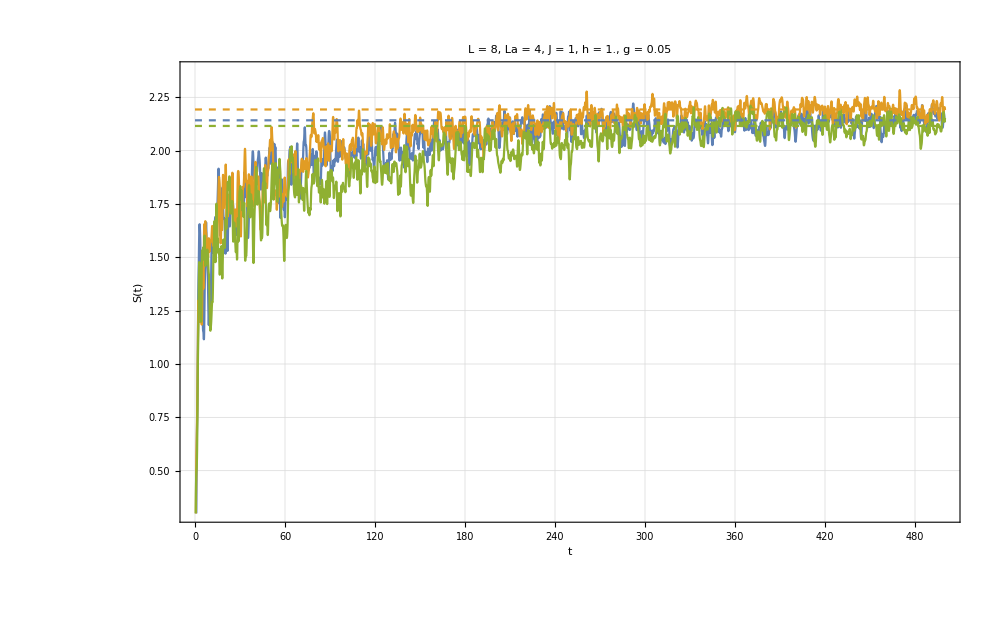

```mathematica
FAKEINFO=SortBy[Transpose[{t1s,sortediprs,limits,energies,productstatesfull,svntproductfull}],First];
fakelimits=FAKEINFO[[All,3]];
Show[{ListPlot[{FAKEINFO[[-3,6]],FAKEINFO[[-2,6]],FAKEINFO[[-1,6]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],Plot[{fakelimits[[-3]],fakelimits[[-2]],fakelimits[[-1]]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Dashed]}]
```

# L = 8, h = 1, minimum h = 0.4

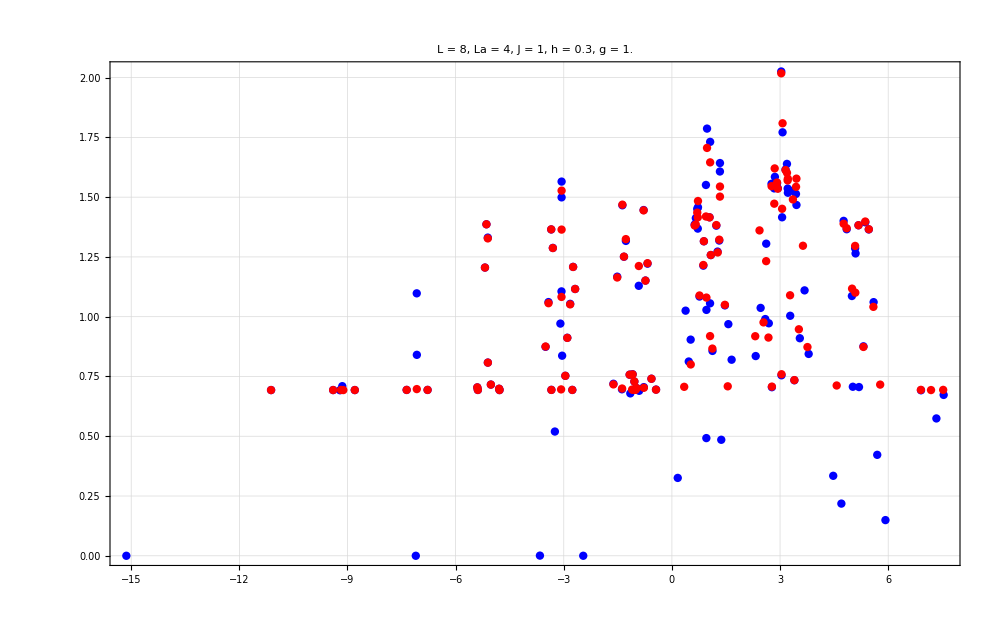

```mathematica
ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Blue,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

```mathematica
tlist=Table[10^i,{i,0,4,0.0010}];
tlist//Length
```

4001

```mathematica
tlist=Table[i,{i,0,2000,0.1}];
tlist//Length
```

20001

```mathematica
allstates=Table[RandomChainProductState[L],100];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]];
```

```mathematica
svntproductfull=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstatesfull},{t,tlist},DistributedContexts->Full,Method->"CoarsestGrained"];
```

## Full RPS vs Positive parity, 100 RPS

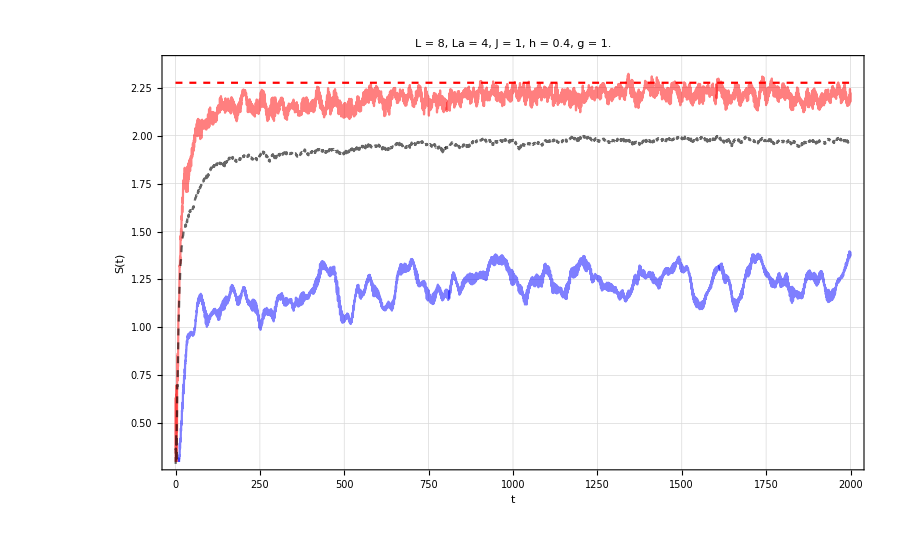

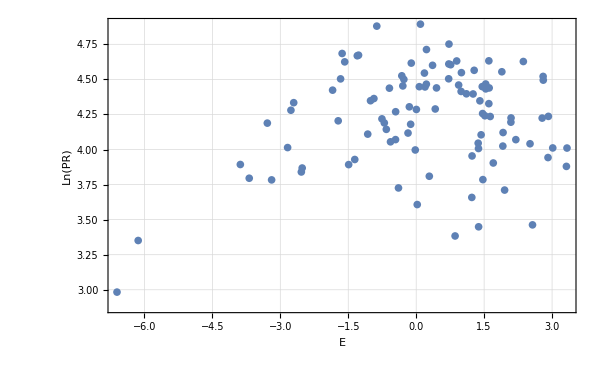

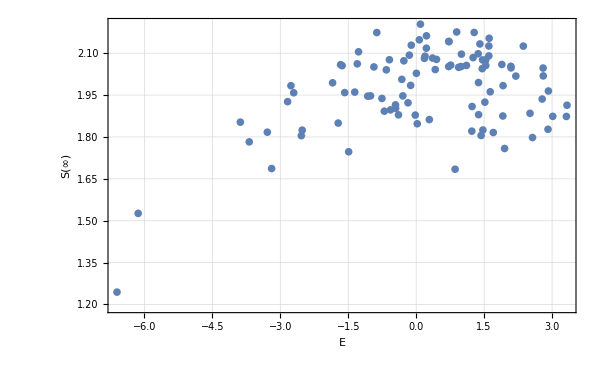

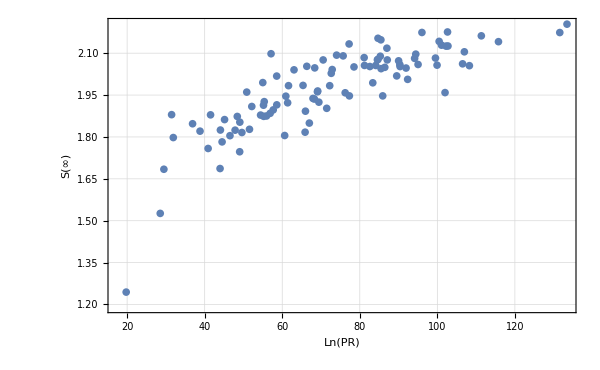

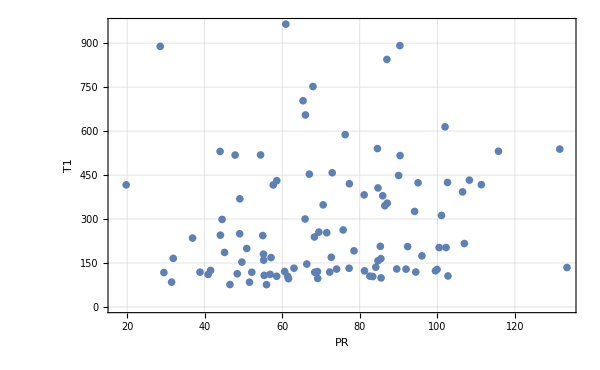

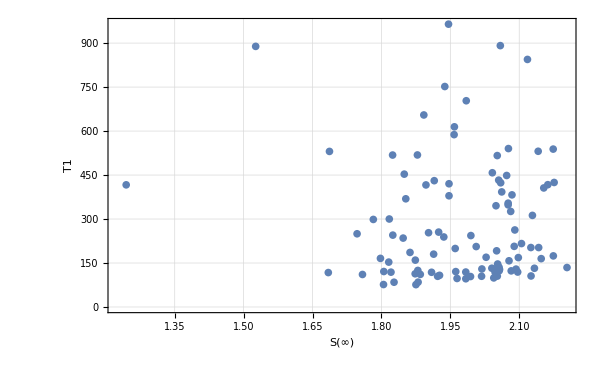

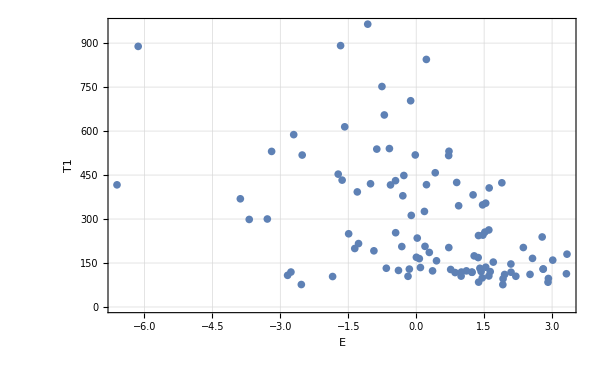

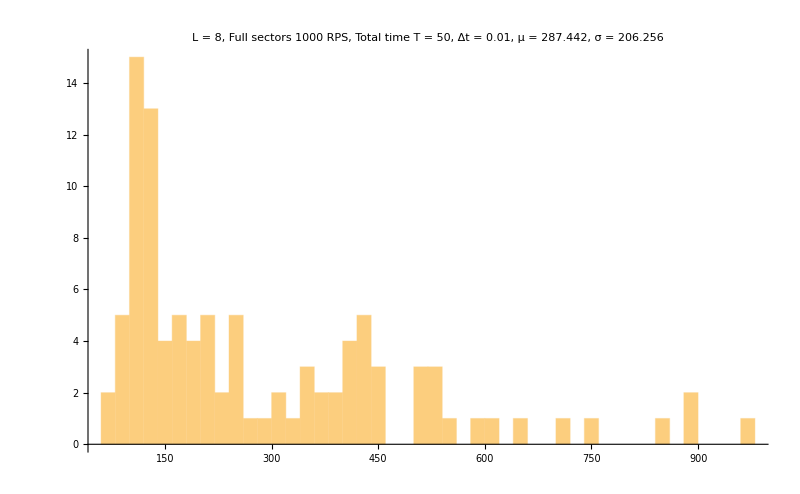

```mathematica
Show[{ListPlot[{svntproductfull[[1]],svntproductfull[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],ListPlot[Mean[svntproductfull],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproductfull[[j]];
times=tlist;
series=list[[All,2]];
limit=Mean[series[[-1000;;-1]]];
position=FirstPosition[series-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstatesfull]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstatesfull},DistributedContexts->Full];
infofull=Transpose[{sortediprs,t1s,limits,energies,productstatesfull}];
unsortedlimits=infofull[[All,3]];
ListPlot[Transpose[{infofull[[All,4]],Log[infofull[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["Ln(PR)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,4]],infofull[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["S(∞)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,1]],infofull[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["Ln(PR)",20,Black],Style["S(∞)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,1]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["PR",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,3]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["S(∞)",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,4]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
Histogram[infofull[[All,2]],50,PlotRange->All,ImageSize->800,PlotLabel->Style["L = 8, Full sectors 1000 RPS, Total time T = 50, Δt = 0.01, μ = "<>ToString[Mean[infofull[[All,2]]]]<>", σ = "<>ToString[StandardDeviation[infofull[[All,2]]]],20,Black]]
```

```mathematica
FAKEINFO=SortBy[Transpose[{t1s,sortediprs,limits,energies,productstatesfull,svntproductfull}],First];
fakelimits=FAKEINFO[[All,3]];
```

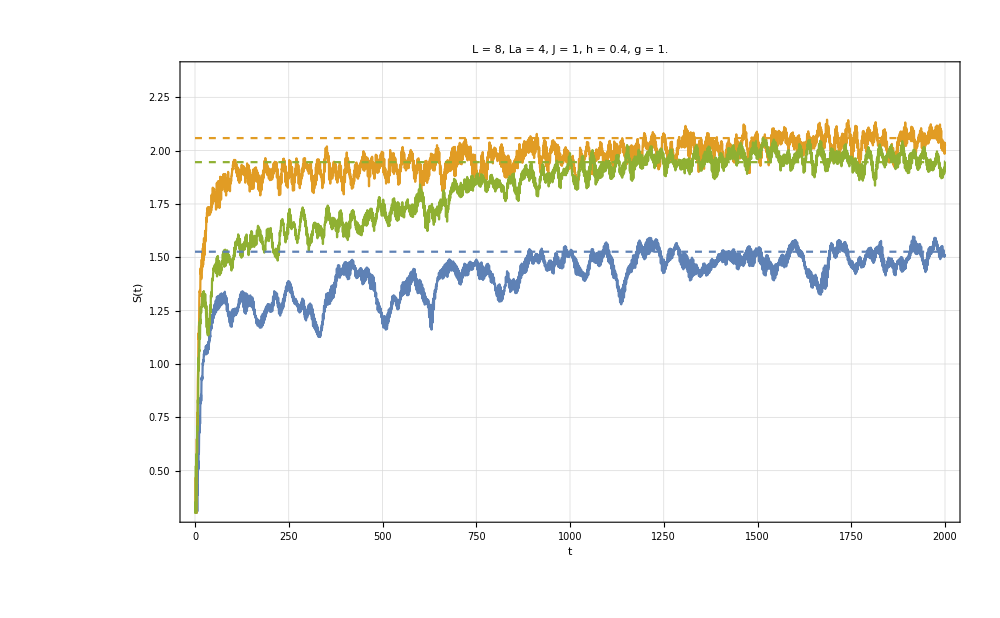

```mathematica
Show[{ListPlot[{FAKEINFO[[-3,6]],FAKEINFO[[-2,6]],FAKEINFO[[-1,6]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],Plot[{fakelimits[[-3]],fakelimits[[-2]],fakelimits[[-1]]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Dashed]}]
```

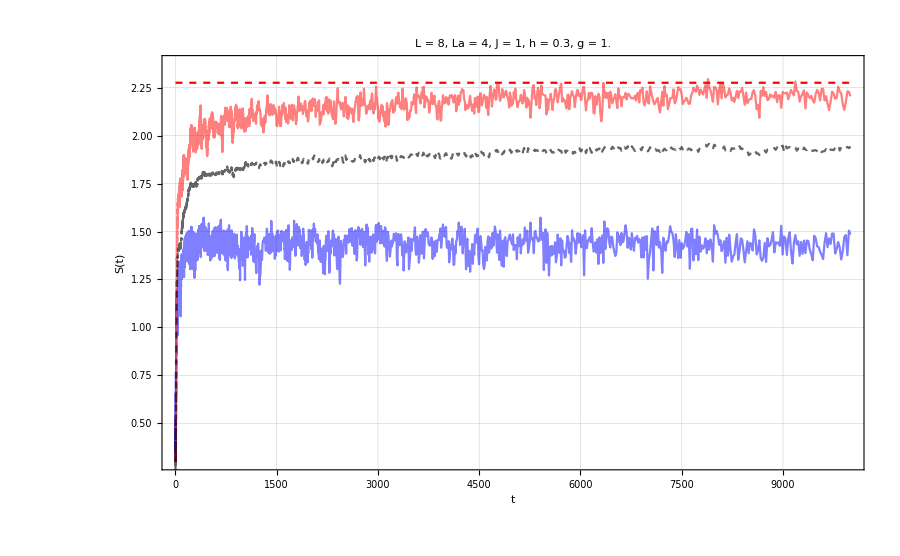

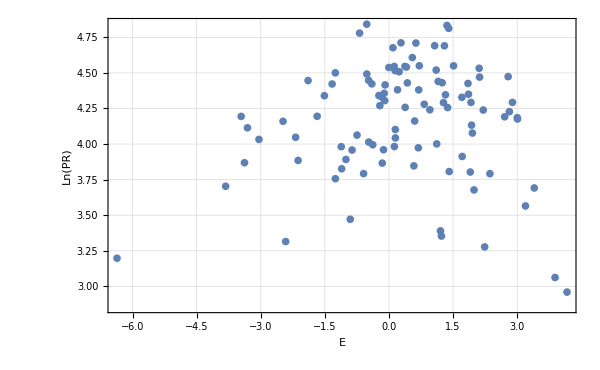

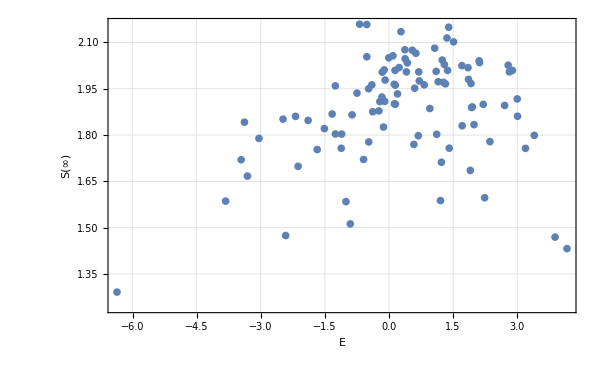

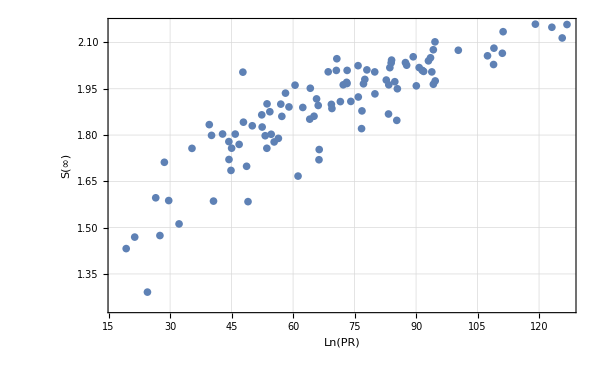

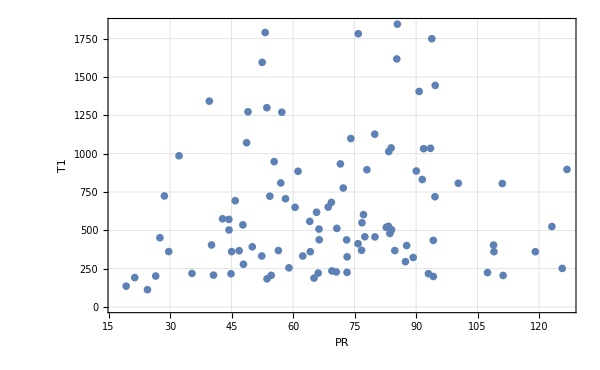

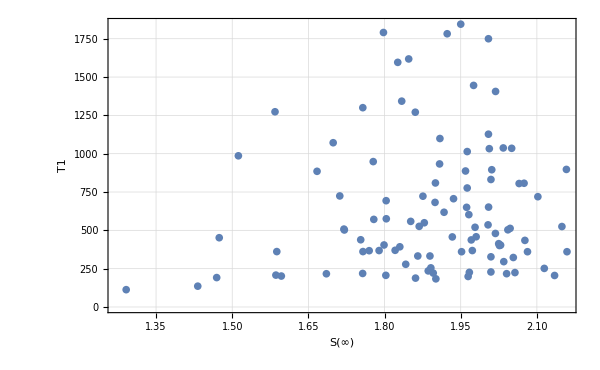

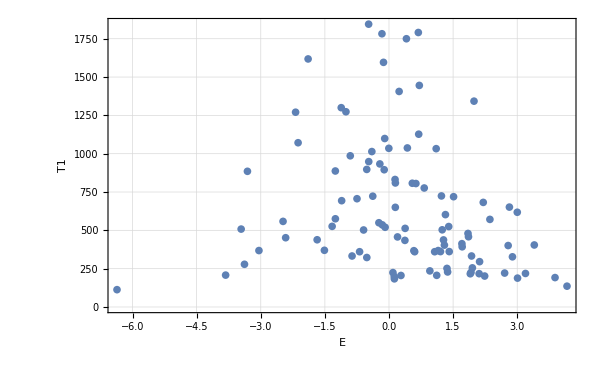

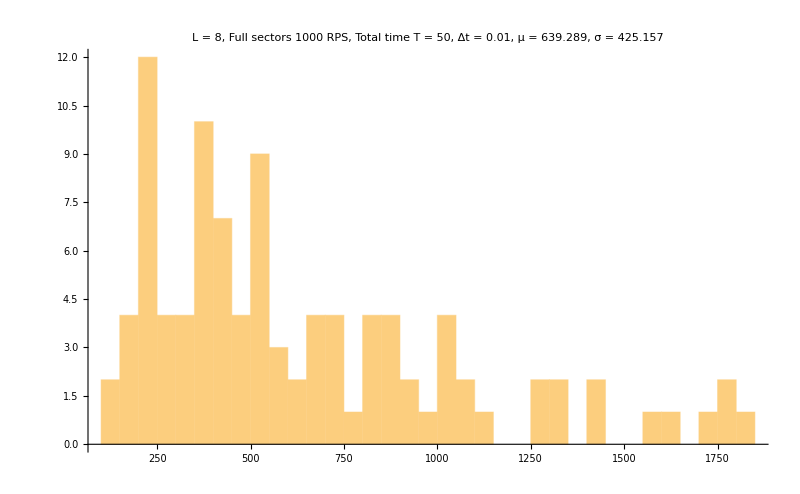

```mathematica
Show[{ListPlot[{svntproductfull[[1]],svntproductfull[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],ListPlot[Mean[svntproductfull],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
t1s={};
limits={};
Do[
list=svntproductfull[[j]];
times=tlist;
series=list[[All,2]];
limit=Mean[series[[-1000;;-1]]];
position=FirstPosition[series-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstatesfull]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstatesfull},DistributedContexts->Full];
infofull=Transpose[{sortediprs,t1s,limits,energies,productstatesfull}];
unsortedlimits=infofull[[All,3]];
ListPlot[Transpose[{infofull[[All,4]],Log[infofull[[All,1]]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["Ln(PR)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,4]],infofull[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["S(∞)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,1]],infofull[[All,3]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["Ln(PR)",20,Black],Style["S(∞)",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,1]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["PR",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,3]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["S(∞)",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{infofull[[All,4]],infofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["E",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
Histogram[infofull[[All,2]],50,PlotRange->All,ImageSize->800,PlotLabel->Style["L = 8, Full sectors 1000 RPS, Total time T = 50, Δt = 0.01, μ = "<>ToString[Mean[infofull[[All,2]]]]<>", σ = "<>ToString[StandardDeviation[infofull[[All,2]]]],20,Black]]
```

```mathematica
FAKEINFO=SortBy[Transpose[{t1s,sortediprs,limits,energies,productstatesfull,svntproductfull}],First];
fakelimits=FAKEINFO[[All,3]];
```

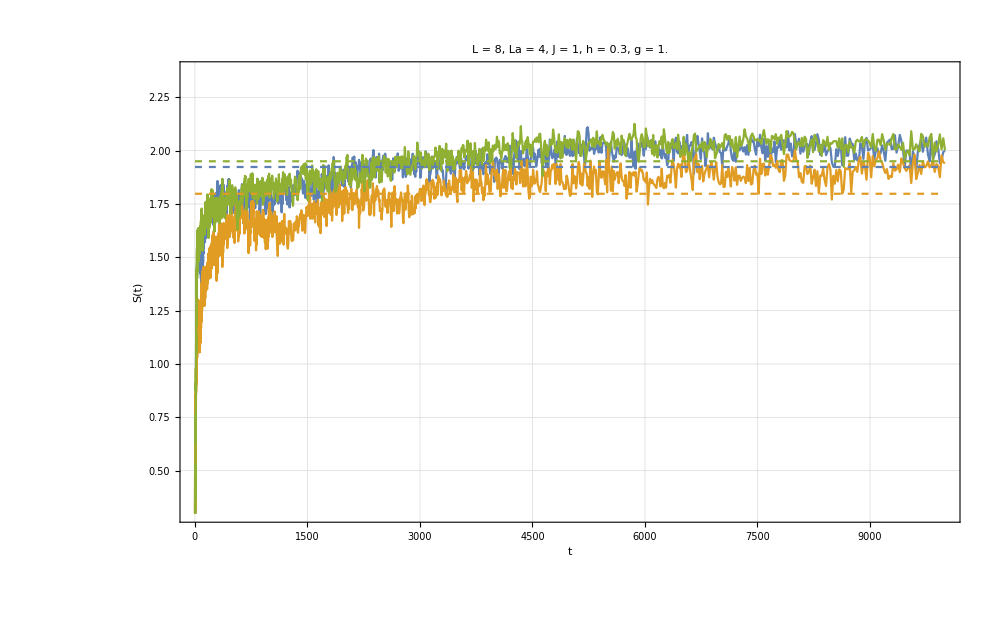

```mathematica
Show[{ListPlot[{FAKEINFO[[-3,6]],FAKEINFO[[-2,6]],FAKEINFO[[-1,6]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],Plot[{fakelimits[[-3]],fakelimits[[-2]],fakelimits[[-1]]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Dashed]}]
```

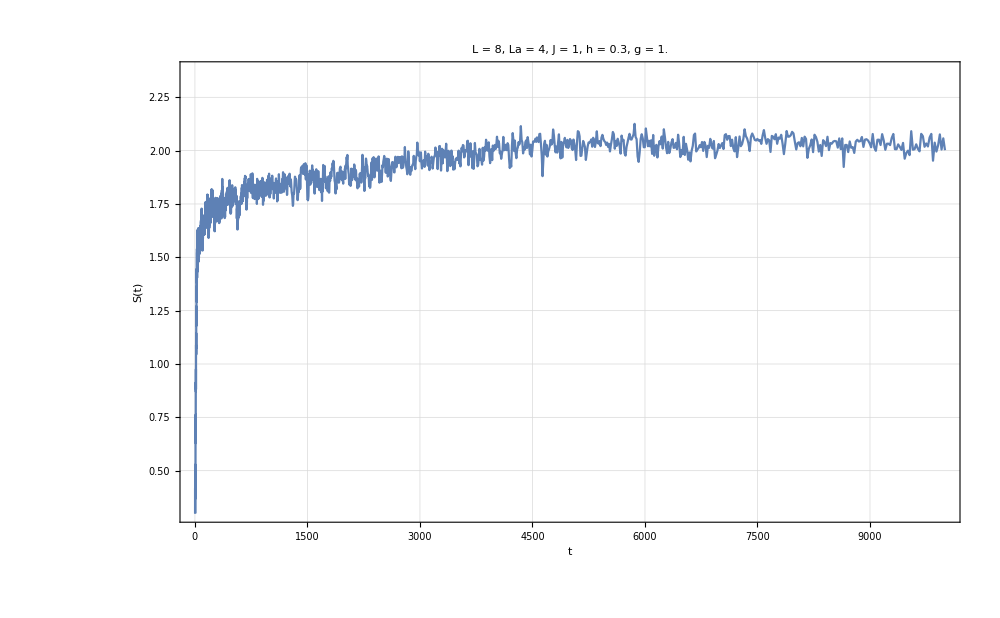

```mathematica
ListPlot[FAKEINFO[[-1,6]],PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}]
```

# Cycle

```mathematica
J=1;
h=1;
La=L/2;
Lb=L-La;
allstates=Table[RandomChainProductState[L],100];
tlist=Table[i,{i,0,1000,0.1}];
```

```mathematica
glist=Table[i,{i,0.05,1,0.01}];
```

```mathematica
g=0.05;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]];
svntproductfull=ParallelTable[{t,svn[L,La,Lb,j,allvals,allvecs,t]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
t1s={};
limits={};
Do[
list=svntproductfull[[j]];
times=tlist;
series=list[[All,2]];
limit=Mean[series[[-1000;;-1]]];
position=FirstPosition[series-limit,x_/;x>0,None];
t1=times[[position[[1]]]];
AppendTo[t1s,t1];
AppendTo[limits,limit];
,{j,Length[productstatesfull]}];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstatesfull},DistributedContexts->Full];
infofull=Transpose[{sortediprs,t1s,limits,energies,productstatesfull}];
unsortedlimits=infofull[[All,3]];
plot=Histogram[infofull[[All,2]],50,PlotRange->All,ImageSize->800,PlotLabel->Style["L = 8, 100 Full RPS, Total time T = 1000, Δt = 0.1, μ = "<>ToString[Mean[infofull[[All,2]]]]<>", σ = "<>ToString[StandardDeviation[infofull[[All,2]]]],20,Black]];
Export["data_t1_h_1_g_"<>ToString[g]<>"_.m",infofull[[All,2]]]
Export["data_saturation_h_1_g_"<>ToString[g]<>"_.m",infofull[[All,2]]]
Export["histogram_h_1_g_"<>ToString[g]<>"_.png",plot]
```